```mathematica
VarVec[n_,name_]:=ToExpression[name<>ToString[#]]&/@Range[n]
```

```mathematica
LeslieMatrix[t_,b_]:=Module[{n=First@Dimensions@b},
	Return[SparseArray[({1,#}&/@Range@n)-> b,{n,n},0]+DiagonalMatrix[t⟦1;;-2⟧,-1]]
	]
```

```mathematica
LefkovitchMatrix[t_,s_,b_]:=DiagonalMatrix[s]+LeslieMatrix[t,b]
```

```mathematica
MatrixSplitting[Population_,indices_,cantidad_]:=Module[{Target,n=First@Dimensions@Population},
	Return@Reverse@{Target=SparseArray[indices->cantidad,{n,n},0],Population-Target}
	]
```

```mathematica
AgeGroups={"Niños","Jovenes","Jovenes Adultos", "Adultos","Adultos Mayores"};
GroupNumber=GP=Length@AgeGroups;
```

```mathematica
Supervivencia=S=VarVec[GP,"s"];(*Probabilidad de Supervivencia*)
Reproduccion=R=VarVec[GP,"r"];(*Probabilidad de Reproduccion*)
```

```mathematica
P=L=LeslieMatrix[S,R];
A=P/.Flatten@{r1->0,r5->0,Thread[S->1],Thread[R->1]};
A=A+A*RandomVariate[NormalDistribution[0.2,0.1],Dimensions@A];
A=A/(Max@A);
{TransitionMatrix,FecundityMatrix}=MatrixSplitting[L,({1,#}&/@Range[GP]),Reproduccion];
PoblacionInicial=Prepend[0&/@Range[GP-1],10000];
```

```mathematica
l=DatosSinteticos=Thread@RecurrenceTable[{Poblacion[n]==A.Poblacion[n-1],Poblacion[1]==PoblacionInicial},Poblacion,{n,GP}];
```

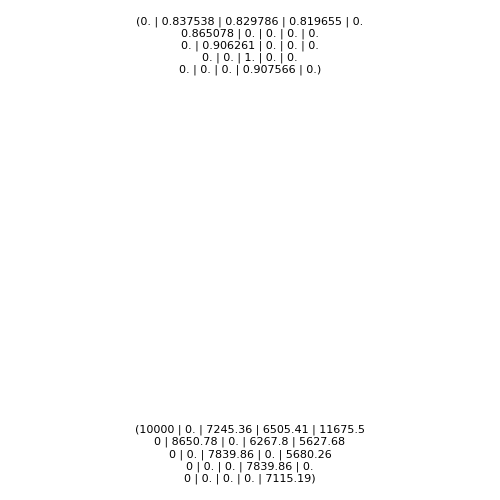

```mathematica
GraphicsColumn[MatrixForm/@{A,DatosSinteticos},ImageSize->{500,500}]
```

```mathematica
Methods={"DecisionTree","GradientBoostedTrees","LinearRegression","NearestNeighbors","NeuralNetwork","RandomForest","GaussianProcess"};
```

```mathematica
l=Predict[Range@5->Diagonal@DatosSinteticos,Method-> #]&/@Methods;
```

```mathematica
lComparePlot[lInterpolada_,DatosSinteticos_,m_]:=Show[ListPlot[Diagonal@DatosSinteticos,PlotMarkers->{Automatic,Offset[10]},PlotRange->Full,PlotLabel->Style[m,Bold,15]],ListLinePlot[lInterpolada[#]&/@Range@GP,DataRange->{1,GP},InterpolationOrder->2]]
```

```mathematica
lErrorPlot[lInterpolada_]:=ListLinePlot[tttt=lInterpolada[#]&/@Range@GP-Diagonal@DatosSinteticos;√(tttt*tttt),PlotStyle->Directive[Thick,Red],Filling->Axis,InterpolationOrder->2,PlotRange->{{1,5},{0,2500}},PlotLabel->Style["Error - Total : "<> ToString[Norm@tttt],13]]
```

```mathematica
level1=Table[lComparePlot[l⟦i⟧,DatosSinteticos,Methods⟦i⟧],{i,Length@l}];
level2=lErrorPlot[#]&/@l;
```

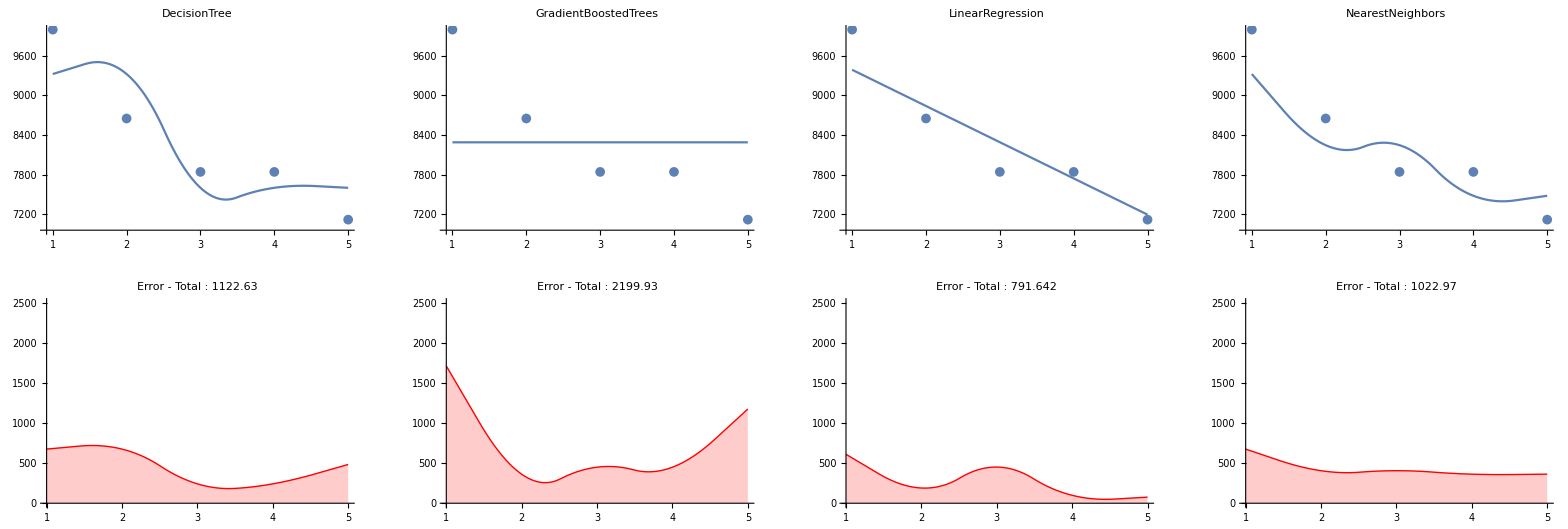

```mathematica
GraphicsGrid[{Append[level1[[1;;4]],LineLegend[{Lighter@Blue,Lighter@Blue,Red},Style[#,13]&/@{"Tabla de Vida","Prediccion","Error"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->30,LegendMarkers->{Graphics[Point[{0,0}]],None,None}]],Append[level2[[1;;4]],SpanFromAbove]},ImageSize->Full]
```

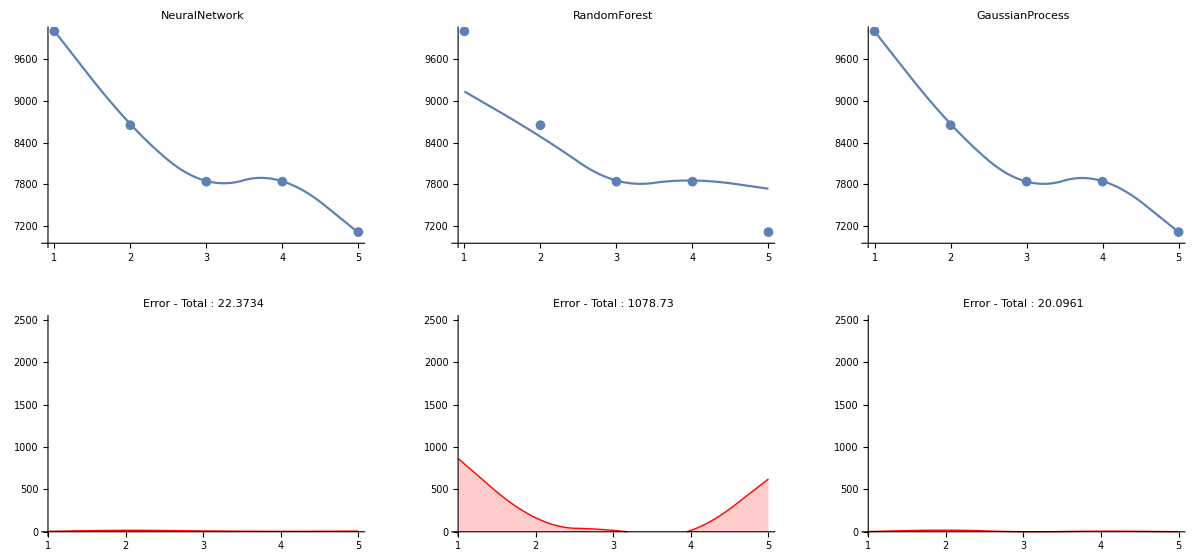

```mathematica
GraphicsGrid[{Append[level1[[5;;-1]],LineLegend[{Lighter@Blue,Lighter@Blue,Red},Style[#,13]&/@{"Tabla de Vida","Prediccion","Error"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->30,LegendMarkers->{Graphics[Point[{0,0}]],None,None}]],Append[level2[[5;;-1]],SpanFromAbove]},ImageSize->Full]
```

```mathematica
bestl=l[[{3,5,7}]];
```

```mathematica
ndx[l_]:=l⟦1;;-2⟧-l⟦2;;-1⟧
```

```mathematica
nqx[l_]:=ndx[l]/l⟦1;;-2⟧
```

```mathematica
nLx[lInterpolada_,a_,b_]:=Quiet@NIntegrate[lInterpolada[t],{t,a,b}]
```

```mathematica
Tx[lInterpolada_,a_]:=nLx[lInterpolada,a,GP]
```

```mathematica
Ex[lInterpolada_,a_]:=Tx[lInterpolada,a]/lInterpolada[a]
```

```mathematica
μ[lInterpolada_,x_]:=-N@(lInterpolada'[x]/lInterpolada[x])
```

```mathematica
dx=ndx[Diagonal@DatosSinteticos];
qx=nqx[Diagonal@DatosSinteticos];
Lx=Table[nLx[#,i,i+1],{i,GP-1}]&/@bestl;
tx=Table[Tx[#,i],{i,GP-1}]&/@bestl;
ex=Table[Ex[#,i],{i,GP}]&/@bestl;
TasaMortalidadEsperada=Table[μ[#,val],{val,1.1,4.9,0.1}]&/@bestl;
```

```mathematica
TableForm[Thread@{Append[dx,0],1-Append[qx,0],15*Append[Table[nLx[Last@bestl,i,i+1],{i,GP-1}],0],15*Append[Table[Tx[Last@bestl,i],{i,GP-1}],0],15*Table[Ex[Last@bestl,i],{i,GP}],Table[μ[Last@bestl,i],{i,GP}]},TableHeadings->{AgeGroups,{"Muertes","Probabilidad de Supervivencia","Años vividos","Años esperados de supervivencia","Esperanza de vida","Tasa de mortalidad instantanea"}},TableAlignments->Center]
```

| Muertes | Probabilidad de Supervivencia | Años vividos | Años esperados de supervivencia | Esperanza de vida | Tasa de mortalidad instantanea
Niños | 1349.22 | 0.865078 | 142025. | 493738. | 49.3838 | 0.00989208
Jovenes | 810.916 | 0.906261 | 121628. | 351713. | 40.5692 | 0.191132
Jovenes Adultos | 0. | 1. | 118426. | 230084. | 29.3453 | -0.000556237
Adultos | 724.673 | 0.907566 | 111658. | 111658. | 14.2295 | 0.0699329
Adultos Mayores | 0 | 1 | 0 | 0 | 0. | 0.015264

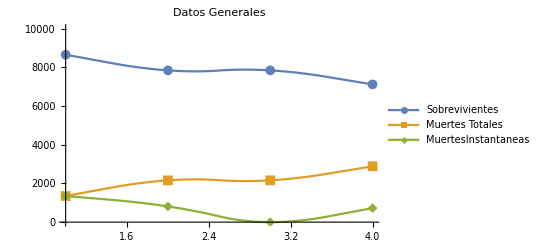

```mathematica
h=10000;
g=0;
ListLinePlot[{Table[h=h-dx[[i]],{i,Length@dx}],Table[g=g+dx[[i]],{i,Length@dx}],dx},PlotRange->{{1,GP-1},{0,10000}},InterpolationOrder->2,PlotLabel->Style["Datos Generales",Bold,16],PlotLegends->{"Sobrevivientes","Muertes Totales","MuertesInstantaneas"},PlotMarkers->{Automatic, 10}]
```

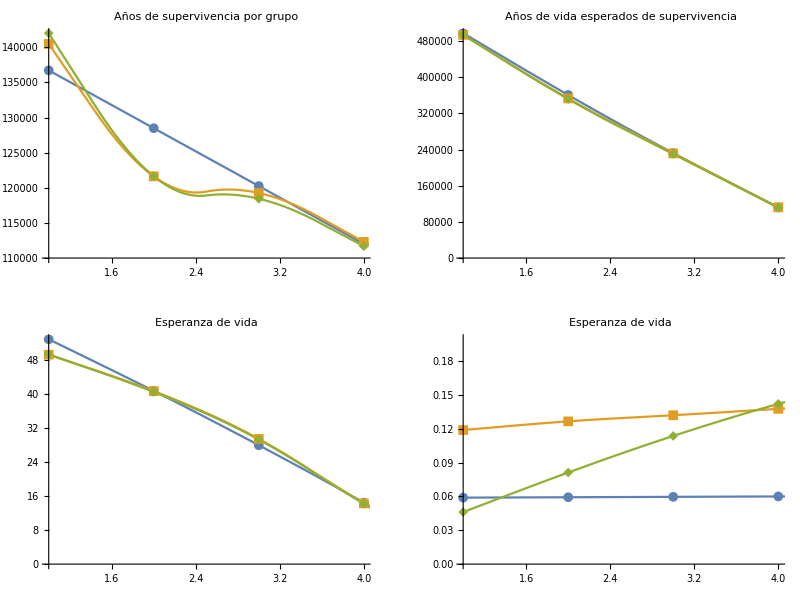

```mathematica
GraphicsGrid[{{ListLinePlot[15*Lx,PlotRange->{{1,GP-1},Automatic},PlotLabel->Style["Años de supervivencia por grupo",Bold,15],InterpolationOrder->2,PlotMarkers->{Automatic, 10}],ListLinePlot[15*tx,PlotRange->{{1,GP-1},Automatic},PlotLabel->Style["Años de vida esperados de supervivencia",Bold,15],InterpolationOrder->2,PlotMarkers->{Automatic, 10}],LineLegend[97,Style[#,13]&/@{"LinearRegression","NeuralNetworks","GaussianProcess"},LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->30]},{ListLinePlot[15*ex,PlotRange->{{1,GP-1},Automatic},PlotLabel->Style["Esperanza de vida",Bold,15],InterpolationOrder->2,PlotMarkers->{Automatic, 10}],ListLinePlot[TasaMortalidadEsperada,PlotRange->{{1,GP-1},{0,Automatic}},PlotLabel->Style["Esperanza de vida",Bold,15],InterpolationOrder->2,PlotMarkers->{Automatic, 10}],SpanFromAbove}},ImageSize->{{1200},{900}}]
```

```mathematica
reproductionRules=NSolve[First[DatosSinteticos][[2;;-1]]== Thread[DatosSinteticos[[1;;-2]]][[1;;-2]].{r1,r2,r3,r4},{r1,r2,r3,r4}];
```

```mathematica
Thread[DatosSinteticos][[1,-2]]
```

0

```mathematica
Thread@DatosSinteticos
```

{{10000,0,0,0,0},{0.,8650.78,0.,0.,0.},{7245.36,0.,7839.86,0.,0.},{6505.41,6267.8,0.,7839.86,0.},{11675.5,5627.68,5680.26,0.,7115.19}}

```mathematica
InterpolateData[l_]:=Interpolation/@l
```

```mathematica
PredictData[l_,m_]:=Predict[Thread[l]⟦1;;-2⟧->#⟦2;;-1⟧,Method->m]&/@l
```

```mathematica
GetA[DatosSinteticos_,lContinua_,PoblacionInicial_]:=Module[{a},
	a=#[Thread[DatosSinteticos]⟦1;;-2⟧]&/@lContinua;
	a=Thread@a;
	Prepend[a,PoblacionInicial]
]
```

```mathematica
ComparePredictionPlot[a_,GP_,DatosSinteticos_,m_]:=Show[ListPlot[DatosSinteticos,PlotMarkers->{Automatic,Offset[10]},PlotRange->Full,PlotLabel->Style[m,Bold,15]],ListLinePlot[Thread@a,DataRange->{1,GP},InterpolationOrder->2]]
```

```mathematica
Error[real_,pred_]:=Norm/@(real-pred)
CompareErrorPlot[a_,DatosSinteticos_]:=ListLinePlot[tttt=Error[Thread@a,DatosSinteticos],PlotStyle->Directive[Thick,Red],Filling->Axis,InterpolationOrder->2,PlotRange->{{1,5},{0,10000}},PlotLabel->Style["Error - Total : "<> ToString[Total@tttt],13]]
```

```mathematica
lContinua1=InterpolateData[DatosSinteticos];
lContinua2=PredictData[DatosSinteticos,"DecisionTree"];
lContinua3=PredictData[DatosSinteticos,"GradientBoostedTrees"];
lContinua4=PredictData[DatosSinteticos,"LinearRegression"];
lContinua5=PredictData[DatosSinteticos,"NearestNeighbors"];
lContinua6=PredictData[DatosSinteticos,"NeuralNetwork"];
lContinua7=PredictData[DatosSinteticos,"RandomForest"];
lContinua8=PredictData[DatosSinteticos,"GaussianProcess"];
```

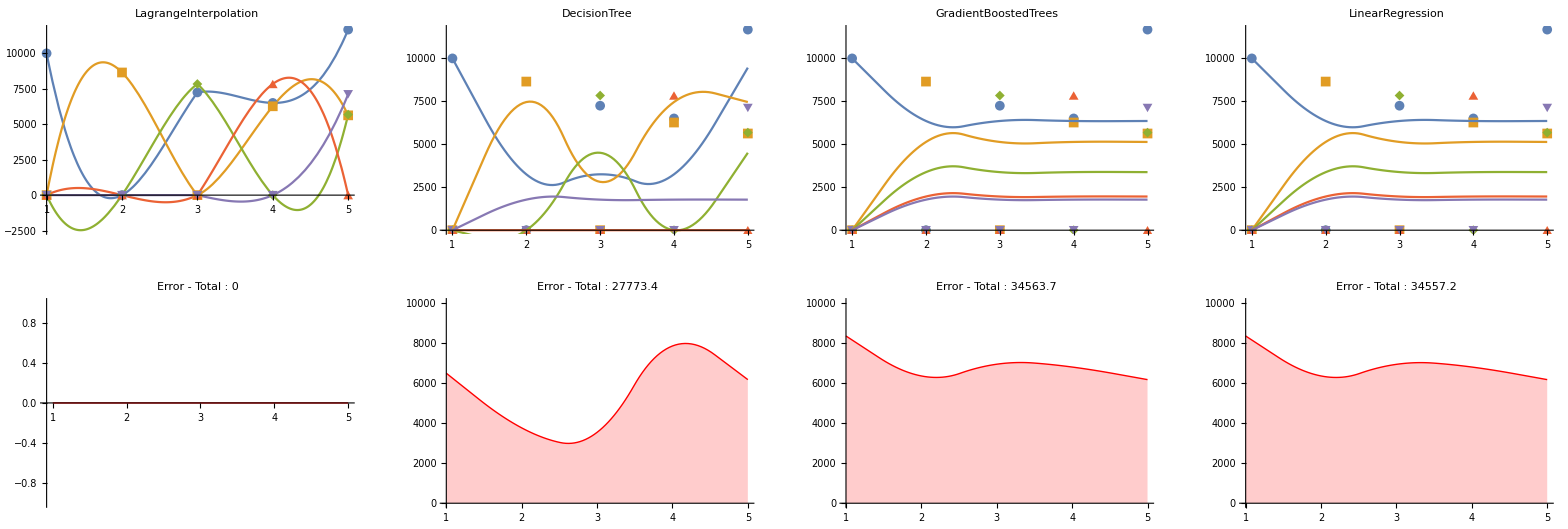

```mathematica
GraphicsGrid[{{
temp=#[t]&/@lContinua1;
a2=GetA[DatosSinteticos,lContinua2,PoblacionInicial];
a3=GetA[DatosSinteticos,lContinua3,PoblacionInicial];
a4=GetA[DatosSinteticos,lContinua4,PoblacionInicial];
Show[Plot[temp,{t,1,5}],ListPlot[DatosSinteticos,PlotMarkers->{Automatic,Offset[10]},PlotRange->Full],PlotLabel->Style["LagrangeInterpolation",Bold,14]],
ComparePredictionPlot[a2,GP,DatosSinteticos,"DecisionTree"],
ComparePredictionPlot[a3,GP,DatosSinteticos,"GradientBoostedTrees"],
ComparePredictionPlot[a4,GP,DatosSinteticos,"LinearRegression"],
LineLegend[97,Style[#,13]&/@AgeGroups,LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->30]},
{
ListLinePlot[Error[Thread@Table[#[i]&/@lContinua1,{i,5}],DatosSinteticos],PlotRange->Full,PlotStyle->Directive[Thick,Red],Filling->Axis,PlotLabel->Style["Error - Total : 0",13]],
CompareErrorPlot[a2,DatosSinteticos],
CompareErrorPlot[a3,DatosSinteticos],
CompareErrorPlot[a4,DatosSinteticos],
SpanFromAbove}},ImageSize->Full]
```

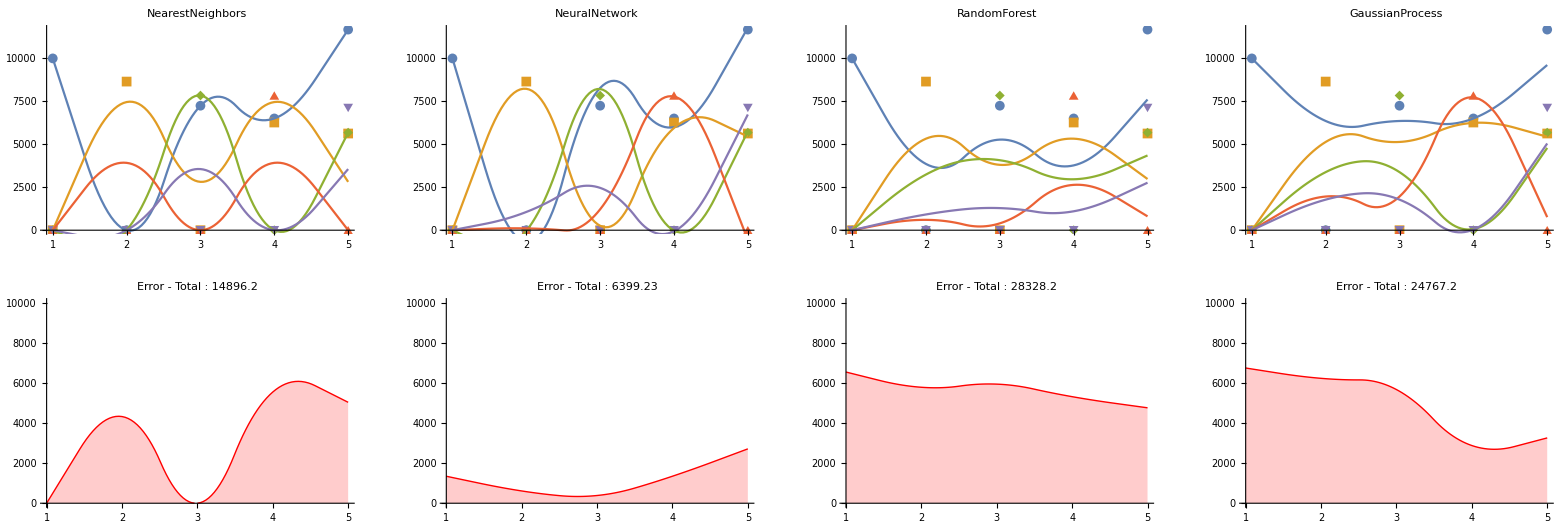

{{0,0.837538,0.829786,0.819655,0},{0.865078,0,0,0,0},{0,0.906261,0,0,0},{0,0,1.,0,0},{0,0,0,0.907566,0}}

```mathematica
GraphicsGrid[{{
a5=GetA[DatosSinteticos,lContinua5,PoblacionInicial];
a6=GetA[DatosSinteticos,lContinua6,PoblacionInicial];
a7=GetA[DatosSinteticos,lContinua7,PoblacionInicial];
a8=GetA[DatosSinteticos,lContinua8,PoblacionInicial];
ComparePredictionPlot[a5,GP,DatosSinteticos,"NearestNeighbors"],
ComparePredictionPlot[a6,GP,DatosSinteticos,"NeuralNetwork"],
ComparePredictionPlot[a7,GP,DatosSinteticos,"RandomForest"],
ComparePredictionPlot[a8,GP,DatosSinteticos,"GaussianProcess"],
LineLegend[97,Style[#,13]&/@AgeGroups,LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->30]},
{CompareErrorPlot[a5,DatosSinteticos],
CompareErrorPlot[a6,DatosSinteticos],
CompareErrorPlot[a7,DatosSinteticos],
CompareErrorPlot[a8,DatosSinteticos],
SpanFromAbove}},ImageSize->Full]
```

```mathematica
%-A
```

{{0.,0.,0.,-1.11022×10^-16,0.},{1.11022×10^-16,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.}}

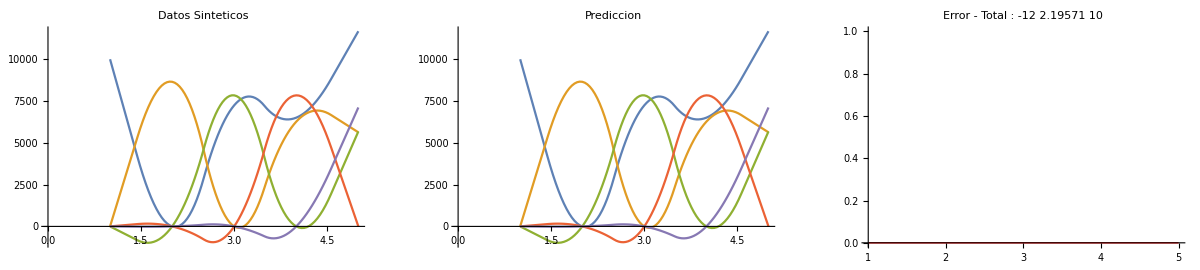

```mathematica
GraphicsRow[{ListLinePlot[DatosSinteticos,InterpolationOrder->2,PlotLabel->Style["Datos Sinteticos",14]],ListLinePlot[d=Thread[RecurrenceTable[{Poblacion[n]==(L/.Flatten@{r1->0,r5->0,reproductionRules,Thread[S[[1;;-2]]->(1-qx)]}).Poblacion[n-1],Poblacion[1]==PoblacionInicial},Poblacion,{n,GP}]],InterpolationOrder->2,PlotLabel->Style["Prediccion",14]],ListLinePlot[yy=Error[d,DatosSinteticos],PlotLabel->Style["Error - Total : "<> ToString[Total@yy],14],PlotStyle->{Thick,Red},PlotRange->{{1,GP},{0,1}}],LineLegend[97,Style[#,13]&/@Append[AgeGroups,"Error"],LegendLayout->"Column",LegendFunction->"Frame",LegendMarkerSize->20]},ImageSize->Full]
```